## Finding wave speed

## Define Parameters and Functions

```mathematica
M = 1;
Q = 0;
q = 1;
r★ =2;
f[r_]:=1-(2 M)/r+Q^2/r^2
fprime[r_]:= D[f[r],r]
```

## Define PDE coefficients

```mathematica
coefTT[r_]:= f[r]-2
coefrr[r_]:=f[r]
coefTr[r_]:=2 (1-f[r])
coefT[r_]:= fprime[r]+(2 f[r]+2 ⅈ q Q -2)/r
coefr[r_]:= fprime[r]+(2 f[r]+2 ⅈ q Q)/r
coef[r_]:=(ⅈ q Q)/r^2
```

## Define Ansatz and PDE

```mathematica
Ψ[T_,r_]:=ⅇ^(ⅈ k r -ⅈ w T)
```

```mathematica
eqn[T_,r_]:= coefTT[r] D[Ψ[T,r],{T,2}]+ coefrr[r] D[Ψ[T,r],{r,2}]+coefTr[r] D[D[Ψ[T,r],r],T]-coefT[r]D[Ψ[T,r],T]+coefr[r] D[Ψ[T,r],r] + coef[r] Ψ[T,r]
```

```mathematica
eqn[T,r]
```

-ⅇ^(ⅈ k r-ⅈ T w) k^2 (1-2/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) k (2/r^2+(2 (1-2/r))/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) (2/r^2+(-2+2 (1-2/r))/r) w+(4 ⅇ^(ⅈ k r-ⅈ T w) k w)/r-ⅇ^(ⅈ k r-ⅈ T w) (-1-2/r) w^2

```mathematica
eqn1[T_,r_]:=Simplify[-ⅇ^(ⅈ k r-ⅈ T w) k^2 (1-2/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) k (2/r^2+(2 (1-2/r))/r)+ⅈ ⅇ^(ⅈ k r-ⅈ T w) (2/r^2+(-2+2 (1-2/r))/r) w+(4 ⅇ^(ⅈ k r-ⅈ T w) k w)/r-ⅇ^(ⅈ k r-ⅈ T w) (-1-2/r) w^2]
```

```mathematica
finaleqn[T_]:=eqn1[T,r★]
```

```mathematica
finaleqn[T]
```

1/2 ⅇ^(2 ⅈ k-ⅈ T w) (w (-ⅈ+4 w)+k (ⅈ+4 w))

## Solve for w and plot phase velocity

```mathematica
solutions1 = w/.NSolve[eqn1[T,r]==0,w]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{(0.5 (-4. k+(0.+2. ⅈ)/r-(1. √(-4.-(0.+8. ⅈ) k r^2-(0.+8. ⅈ) k r^3+4. k^2 r^4))/r))/(2.+r),(0.5 (-4. k+(0.+2. ⅈ)/r+(√(-4.-(0.+8. ⅈ) k r^2-(0.+8. ⅈ) k r^3+4. k^2 r^4))/r))/(2.+r)}

```mathematica
w1:= solutions1[[1]]
w2:= solutions1[[2]]
```

```mathematica
Plot3D[Re[w1]/k, {k,0,10},{r,1,10},PlotStyle->Directive[Orange,Opacity[0.2]],PlotRange->All, AxesOrigin->{0,0},AxesLabel->{HoldForm[k],HoldForm[r],HoldForm[c]},PlotLabel->"Phase Velocity Plot 3D: Branch 1",LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

```mathematica
Plot3D[Re[w2]/k, {k,0,10},{r,1,10},PlotStyle->Directive[Blue,Opacity[0.2]],PlotRange->All, AxesOrigin->{0,0},AxesLabel->{HoldForm[k],HoldForm[r],HoldForm[c]},PlotLabel->"Phase Velocity Plot 3D: Branch 2",LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

```mathematica
solutions2 = w/.NSolve[finaleqn[T]==0,w]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{0.125 ((0.+1. ⅈ)-4. k-1. √(-1.-(0.+24. ⅈ) k+16. k^2)),0.125 ((0.+1. ⅈ)-4. k+√(-1.-(0.+24. ⅈ) k+16. k^2))}

```mathematica
w3= solutions2[[1]]
w4 = solutions2[[2]]
```

0.125 ((0.+1. ⅈ)-4. k-1. √(-1.-(0.+24. ⅈ) k+16. k^2))

0.125 ((0.+1. ⅈ)-4. k+√(-1.-(0.+24. ⅈ) k+16. k^2))

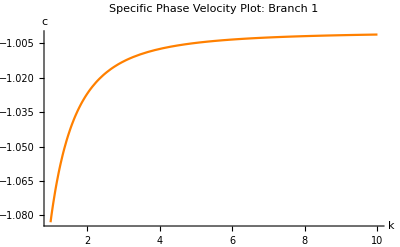

```mathematica
Show[{Plot[Re[w3]/k, {k,0,10},PlotStyle->Orange]},PlotRange->All, AxesLabel->{HoldForm[k],HoldForm[c]},PlotLabel->"Specific Phase Velocity Plot: Branch 1",LabelStyle->{GrayLevel[0]}]
```

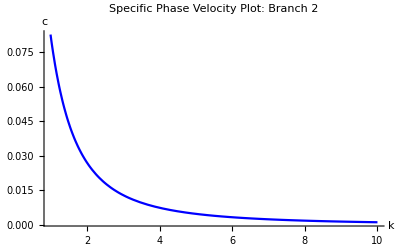

```mathematica
Show[{Plot[Re[w4]/k, {k,0,10},PlotStyle->Blue]},PlotRange->All, AxesLabel->{HoldForm[k],HoldForm[c]},PlotLabel->"Specific Phase Velocity Plot: Branch 2",LabelStyle->{GrayLevel[0]}]
```

## Plot Group Velocity

```mathematica
g1=Re[D[w1,k]];
```

```mathematica
g2=Re[D[w2,k]];
g3=Re[D[w3,k]];
g4=Re[D[w3,k]];
```

```mathematica
Plot3D[g1 ,{k,0,10},{r,1,10},PlotStyle->Directive[Orange,Opacity[0.2]],PlotRange->All, AxesOrigin->{0,0},AxesLabel->{HoldForm[k],HoldForm[r],HoldForm[c]},PlotLabel->"Group Velocity Plot 3D: Branch 1",LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

```mathematica
Plot3D[g2 ,{k,0,10},{r,1,10},PlotStyle->Directive[Blue,Opacity[0.2]],PlotRange->All, AxesOrigin->{0,0},AxesLabel->{HoldForm[k],HoldForm[r],HoldForm[c]},PlotLabel->"Group Velocity Plot 3D: Branch 2",LabelStyle->{GrayLevel[0]}]
```

-Graphics3D-

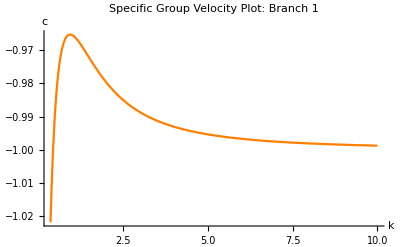

```mathematica
Show[{Plot[g3, {k,0,10},PlotStyle->Orange]},PlotRange->All, AxesLabel->{HoldForm[k],HoldForm[c]},PlotLabel->"Specific Group Velocity Plot: Branch 1",LabelStyle->{GrayLevel[0]}]
```

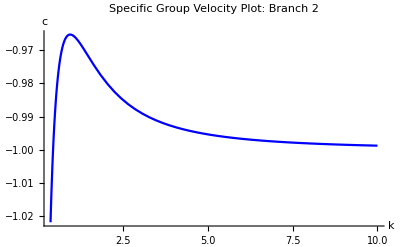

```mathematica
Show[{Plot[g4, {k,0,10},PlotStyle->Blue]},PlotRange->All, AxesLabel->{HoldForm[k],HoldForm[c]},PlotLabel->"Specific Group Velocity Plot: Branch 2",LabelStyle->{GrayLevel[0]}]
```